# parton.note.1.nb

```mathematica
NotebookFileName[]
```

D:\gitstorage\note\parton-df\parton.note.1.nb

## notation

k^+→k`p, k^-→k`m,k_⊥=k`perp,

Ω_ϕ→Ω`ϕ

baryon→ba

mesons→ϕ

## definition

d`ϕ[k_]:=k^2-(m`ϕ)^2+I ϵ==k`p*k`m-k`perp-(m`ϕ)^2+I ϵ==k`p*k`m-Ω`ϕ+I ϵ

d`ba[k_]:=(p-k)^2-(m`ba)^2+I ϵ==(p-k)`p*(p-k)`m-k`perp-(m`ba)^2+I ϵ==(p-k)`p*(p-k)`m-(Ω`ba)^2+I ϵ

Ω`ϕ:=(k`perp)^2+(m`ϕ)^2≥0

Ω`ba:=(k`perp)^2+(m`ba)^2≥0

k`p*k`m-(k`perp)^2=(m`ϕ)^2

p`p*p`m-(p`perp=0)^2=(m`ba)^2

## test

```mathematica
mass`rule={
Ω`ϕ->(k`perp)^2+(m`ϕ)^2,Ω`ba->(k`perp)^2+(m`ba)^2,
k`p->y*p`p,p`m->(m`ba)^2/p`p
};
```

```mathematica
(
(
(p`p-k`p)*k`p*((p`m-(Ω`ϕ)/(k`p))-(Ω`ba)/(p`p-k`p))
)//.mass`rule
)//Simplify
```

-p`p ((k`perp)^2+(m`ba)^2 y^2-(-1+y) (m`ϕ)^2)

## integral Z0

(∫^∞)_(-∞)ⅆk`m 1/(D`ϕ)==(∫^∞)_(-∞)ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)

Simplify notation a little

((∫ⅆz)^∞)_(-∞)1/(z-a+I ϵ),a≥0

## if k`p > 0

单极点在 1/(k`p)(Ω_ϕ-I ϵ),(第四象限), 做一个顺时针的闭合回路，积分共有两部分，利用留数定理。

ParametricPlot[{{Cos[t],Sin[t]},{(2(t-3π/2))/π,0}},{t,π,2π}]

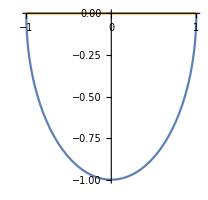

int+(∫_0)^-π(I R e^(I φ) ⅆφ)/(R e^(I φ)-a+I ϵ)+→

int+(∫_0)^(-π/2)(I R e^(I φ) ⅆφ)/(R e^(I φ)-a)=-2π I *(1)

```mathematica
int`b=Assuming[{R>a>ϵ>0},
Simplify[Integrate[I R Exp[I φ]/(R Exp[I φ]-a+I ϵ),{φ,0,-π}]]
]
```

-ⅈ π+2 ArcTanh[(a-ⅈ ϵ)/R]

## add and simplify

```mathematica
int`b`simlif=Assuming[{R>a>0},
Limit[int`b,ϵ->0,Direction->"FromAbove"]
]//Simplify
```

-ⅈ π+2 ArcTanh[a/R]

```mathematica
int`result=Assuming[{R>a>0},
(-2π I-int`b`simlif)/.{a->li*R}//Simplify
]
```

-ⅈ π-2 ArcTanh[li]

so,

int`result→-ⅈ π-2 ArcTanh[li]→(R→+∞,a/R→0)→-ⅈ π

## apply

∫ⅆk`m 1/(D`ϕ)==∫ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ),

∫ⅆz/(z-a+I ϵ)==-ⅈ π,a≥0

******************************************

∫ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)→

if y≠0, then

→1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)→1/(k`p)∫ⅆz 1/(z-Ω`ϕ+I ϵ)→

1/(k`p)(-ⅈ π)→(-ⅈ π)1/y 1/(p`p)

## if k`p = 0

(∫^∞)_(-∞)ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)→1/(-Ω`ϕ+I ϵ)(∫^∞)_(-∞)ⅆk`m→∞ (k`p=0)

## if k`p < 0

单极点在 1/(k`p)(Ω_ϕ-I ϵ)(第二象限), 做一个顺时针的闭合回路，积分共有两部分，利用留数定理。

积分回路中不包含极点，所以和为0

ParametricPlot[{{Cos[t],Sin[t]},{(2(t-3π/2))/π,0}},{t,π,2π}]

-Graphics-

int+(∫_0)^-π(I R e^(I φ) ⅆφ)/(R e^(I φ)-a+I ϵ)+→

int+(∫_0)^(-π/2)(I R e^(I φ) ⅆφ)/(R e^(I φ)-a)=0

so,

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)==-1/(k`p)(∫_0)^-π arc==-1/(k`p)(-ⅈ π)==1/(k`p)ⅈ π

**************************************************

## conclusion

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)

k`p*k`m-Ω`ϕ+I ϵ, can be written as,

k`p*(k`m-(Ω`ϕ-I ϵ)/(k`p)),

********************

k`p>0,

(k`p+I δ Ω`ϕ)(k`m-((Ω`ϕ)/(k`p)-I k`p δ))→第四象限

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))

k`p k`m- Ω`ϕ==k^2-(m`ϕ)^2+I ϵ≥0, 在积分之后,写成费曼截面的时候,总是正的--on shell

so,ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))always positive, can be noted as ⅈ ϵ,

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))→k`p k`m -Ω`ϕ+ⅈ ϵ

**************************************

k`p<0,

(k`p-I δ Ω`ϕ)(k`m-((Ω`ϕ)/(k`p)-I k`p δ))→第二象限

k`m k`p-Ω`ϕ+ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ))

ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ)) always positive ,can be noted as ⅈ ϵ,

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ))→k`p k`m -Ω`ϕ+ⅈ ϵ

****************************************

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)→ (-ⅈ π θ[k`p])/(k`p+I δ Ω`ϕ)+(ⅈ π θ[-k`p])/(k`p-I δ Ω`ϕ),δ→0

其中θ[k`p]是阶跃函数

*********************

## integral A0

ii=∫ⅆ^2 k 1/(k^2-m^2+I ϵ)=1/2∫_(-∞)^∞ ⅆk`p∫_(-∞)^∞ ⅆk`m 1/(k`p k`m-m^2+I ϵ)

Few - Body Syst (2012) 52 : 421–426,light - front dynamics (LFD)

a simple example of two - dimensional loop amplitude for a particle of mass m :

In the covariant approach, this amplitude can be computed by dimensional regulation and is given by

ii=-I π(2/(2-d)-Log[π]-γ+O[2-d]-Log[m^2/μ^2])

where μ is a mass parameter introduced to give the correct mass dimensions in d dimensions, 
γ ≈ 0.577 is  Euler' s constant, 
and d goes to 2 in this example

The LNA behavior of this amplitude in the limit m→0 is thus given by I[LNA]=I π log[m^2].

In time - ordered perturbation theory, it is straightforward to use Cauchy' s integral theorem and compute the amplitude as follows :

ii=∫ⅆ k^1ⅆ k^0 1/((k^0+ω_k-I ϵ)(k^0-ω_k+I ϵ))→Lower halp plane

-2π I∫_(-∞)^(Λ→ ∞) ⅆ k^1*1/(2 √((k^1)^2+m^2))→-2π I∫_0^(Λ→ ∞) ⅆ k^1*1/(√((k^1)^2+m^2))→

(-2π I)(-1/2 Log[1-k/(√(k^2+m^2))]+1/2 Log[1+k/(√(k^2+m^2))])@{0,Λ→+∞}→

(-2π I)(-1/2Log[m^2/(2 Λ^2)]+1/2 Log[2] )→ (2π I)(1/2 Log[m^2/(2 Λ^2)]-1/2 Log[2] )

lim_(Λ→∞)  π I Log[m^2/(2Λ)^2]

in which, ω_k=√((k^1)^2+m^2)

The LNA behavior of this amplitude is identical to ILNA=π I Log[m^2].

## LFD calculation

However, the LFD calculation of this amplitude is not so simple due to a dramatic change of pole structure

A0=∫ⅆ^2 k 1/(k^2-m^2+I ϵ)

A0=1/2*∫_(-∞)^∞ ⅆk`p∫_(-∞)^∞ ⅆk`m 1/(k`p k`m-m^2+I ϵ)→

=1/2*∫_(-∞)^∞ ⅆk`p∫_(-∞)^∞ ⅆu/u 1/(k`p -(m^2-I ϵ)u)

=1/2*∫_(-∞)^∞ ⅆk`p∫_(-∞)^∞ ⅆu*1/2(1/(u+I δ)+1/(u-I δ))1/(k`p -(m^2-I ϵ)u)→

in which, u=1/(k`m),

*******************************************************

and in the last line split the 1/u denominator  into two poles off the real u axis.

This split produces just the correct result, as we shall see. 
Before applying this form to our integrals, we make a final step for the tadpole.

After the k`m integration has been carried out, which can be done safely using the residue theorem as the integral over u is convergent,

a divergent k`p integral appears that must be regulated.

We do that by using a finite cutoff. The result is,

*******************************************************

cauchy theorem→

if k`p>0, singularity{0,-I δ,Iδ,(k`p)/(m^2-I ϵ)(first quadrant)}

if k`p<0, singularity{0,-I δ,Iδ,(k`p)/(m^2-I ϵ)(third quadrant)}

*****************************************

if k`p>0,

1/2*∫_(-∞)^∞ ⅆk`p(-2π I)*1/2 1/(k`p -(m^2-I ϵ)(-I δ))θ(k`p)
if k`p<0,

1/2*∫_(-∞)^∞ ⅆk`p(+2π I)*1/2 1/(k`p -(m^2-I ϵ)(I δ))θ(-k`p)

*********************************

A0=1/2*∫_(-∞)^∞ (ⅆk`p(-I π )(θ(k`p))/(k`p +I δ m^2)+(+I π )(θ(-k`p))/(k`p -I δ m^2))→

∫_0^∞ ⅆk`p(-I π)/(k`p +I δ m^2)→lim_(Λ→+∞) ∫_0^Λ ⅆk`p(-I π)/(k`p +I δ m^2)→

lim_(Λ→+∞) (-I π )Log[k`p+I δ m^2]@{Λ,0}→

(-I π )(Log[Λ+I δ m^2]-Log[I δ m^2])==(-I π )(Log[Λ/I δ]-Log[m^2])

This may be compared to the result from dimensional regularization

A0=-I π(1/ϵ-γ+Log[4π]-Log[m^2/μ^2])+O[ϵ]

Clearly, the correct dependence on the mass of the covariant amplitude is reproduced by the LF calculation

## cylindrical coordinates

ii=∫ⅆ^2 k 1/(k^2-m^2+I ϵ)==1/2∫_(-∞)^∞ ⅆk`p∫_(-∞)^∞ ⅆk`m 1/(k`p k`m-m^2+I ϵ)==1/2∫_(-∞)^∞ (ⅆk`p)/(k`p)∫_(-∞)^∞ ⅆk`m 1/(k`m-(m^2-I ϵ)/k`p)

We may use the LF cylindrical coordinates

(k`p=r Cos[φ], k`m=r Sin[φ]) to perform the k`p and k`m integration as follows:

ii==1/2∫_0^∞ ⅆr r∫_0^(2π) ⅆϕ(r^2 Sin[ϕ]Cos[ϕ]-m^2+I ϵ)^-1==lim_(R→+∞) (I π Log[(2 m^2)/(R^2 Exp[-I π/2])]+O[1/R^4])

where R is the cutoff parameter in the LF cylindrical coordinate integration.

The result correctly yields ii`LNA=I π Log[m^2],

identical to the results of the covariant and equal - time calculations. It demonstrates the equivalence of the LF formalism to the equal time and covariant formulations.

## cylindrical coordinates approach

ii==1/2∫_0^∞ ∫_0^(2π) rⅆr ⅆϕ*1/(r^2 Sin[ϕ]Cos[ϕ]-m^2+I ϵ)→

1/2∫_0^∞ ∫_0^(2π) ⅆr/r ⅆϕ*1/(Sin[ϕ]Cos[ϕ]-m^2/r^2+I ϵ)→{Sin[ϕ]Cos[ϕ]=1/2 Sin[2ϕ],set θ=2ϕ}→

1/2∫_0^∞ ∫_0^(4π) ⅆr/r ⅆθ*1/(Sin[θ]-2m^2/r^2+I ϵ)

We proceed by performing the integration in the complex plane.

**********************************

If we let z=Exp[I θ] and define β=2m^2/r^2  the integration becomes

∫_0^∞ ⅆr/r∫_C  ⅆz*2/((z-(I β+√(1-β^2)+ϵ))(z-(I β-√(1-β^2)+ϵ)))

(z-(I β+√(1-β^2)+ϵ))(z-(I β-√(1-β^2)+ϵ))==-1+z^2-2 ⅈ z β-2 z ϵ+2 ⅈ β ϵ+ϵ^2→

-1+z^2-2 ⅈ z β-2 z ϵ+2 ⅈ  ϵ→

-1+Exp[2I θ]-2 ⅈ Exp[I θ] *2m^2/r^2-2 Exp[I θ] ϵ+2 ⅈ  ϵ→

Exp[I θ](-Exp[-θ]+Exp[θ]-2 ⅈ * 2m^2/r^2-2  ϵ+2 Exp[-I θ]ⅈ  ϵ)→

2ⅈ Exp[I θ]( Sin[θ]- 2m^2/r^2+ⅈ ϵ+Exp[-I θ]ϵ)→suppose Exp[-I θ]ϵ can be dropped→

2ⅈ Exp[I θ]( Sin[θ]- 2m^2/r^2+ⅈ ϵ)

**********************************

ⅆz*2/((z-(I β+√(1-β^2)+ϵ))(z-(I β-√(1-β^2)+ϵ)))→

I Exp[I θ]ⅆθ*2/(2ⅈ Exp[I θ]( Sin[θ]- 2m^2/r^2+ⅈ ϵ))→ⅆθ*1/( Sin[θ]- 2m^2/r^2+ⅈ ϵ)

1/2∫_0^(4π) ⅆθ*1/(Sin[θ]-2m^2/r^2+I ϵ)== 1/2*2∫_0^(2π) ⅆθ*1/(Sin[θ]-2m^2/r^2+I ϵ)→
∫_C  ⅆz*2/((z-(I β+√(1-β^2)+ϵ))(z-(I β-√(1-β^2)+ϵ)))

where C represents integration around the unit circle in the counter-clockwise direction.

**************************so,

Since β can possess any value between 0 and ∞ we must consider the possible cases carefully.

0≤β≤1,

the poles lie on the unit circle in the upper half - plane.
Epsilon shifts these poles in the positive direction, such that the pole in the first quadrant now lies outside the contour of integration, while the pole in the second quadrant lies within the contour of integration.
Performing the integration gives

∫_C  ⅆz*2/((z-(I β+√(1-β^2)+ϵ))(z-(I β-√(1-β^2)+ϵ)))→

2π I 2/((I β-√(1-β^2)+ϵ)-(I β+√(1-β^2)+ϵ))== 2π I 2/(-2 √(1-β^2))==(2π I)/(-√(1-β^2))

*************so,

ii==∫_0^∞ ⅆr/r*(-2π I)/(√(1-β^2)),0≤β≤1,

**********************

in the case where β>1,the poles move onto the imaginary axis.They are now

I(β±√(β^2-1))+ϵ

Since β>1 we can write β=1+η. Substituting this into the poles gives

I(1+η±√(η(η+2η)))+ϵ

Written this way it is clear that the pole with the minus sign lies inside the unit circle, 
while the pole with the plus sign lies outside the unit circle.
Again performing the contour integration yields:

∫_C  ⅆz*2/((z-(I β+√(1-β^2)+ϵ))(z-(I β-√(1-β^2)+ϵ)))→

2π I 2/((I β-√(1-β^2)+ϵ)-(I β+√(1-β^2)+ϵ))== 2π I 2/(-2 √(1-β^2))==(-2π I)/(√(1-β^2))

*************so,

ii==∫_0^∞ ⅆr/r*(-2π I)/(√(1-β^2)),0≤β≤1,

Therefore,in both cases we obtain the same result for ii,

Substituting back in the definition of β,and proceeding with the r integration,we get

ii==∫_0^∞ ⅆr/r*(-2π I)/(√(1-β^2)) ,β=2m^2/r^2→

ii==(-2π I)∫_0^∞ ⅆr/r 1/(√(1-(2m^2/r^2)^2))==(-2π I)∫_0^∞ ⅆr/r r^2/(r √(r^4-4 m^4))==(-2π I)∫_0^∞ ⅆr r/(√(r^4-4 m^4))→

(-2π I)lim_(R→+∞) ∫_0^R ⅆr r/(√(r^4-4 m^4))→

(-π I)lim_(R→+∞) ArcTanh[R^2/(√(R^4-4 m^4))]→

(-π I)lim_(R→+∞) ArcTanh[1/(√(1-4m^4/R^4))]

Substituting a series expansion for the hyperbolic arctangent function gives the final result

(-π I)lim_(R→+∞) ArcTanh[1/(√(1-4m^4/R^4))]→

(-π I)lim_(R→+∞) ArcTanh[1/(√(1-4m^4/R^4))]→

ii=-I π Log[R^2]-π^2/2+I π Log[m^2]+O[1/R^4]

## ArcTanh

```mathematica
Series[ArcTanh[x],{x,1,2},Assumptions->(x>1)]
Sum[x^(2n-1)/(2n-1),{n,1,Infinity}]
```

```mathematica
TrigToExp[ArcTanh[z]]
```

-1/2 Log[1-z]+1/2 Log[1+z]

so, its expansion @ z==1, get a pole can’t write in  power series.

Instead,

********************************

```mathematica
Series[
ArcTanh[x],
{x,1,1}
]
```

-ⅈ (π Floor[-Arg[-1+x]/(2 π)]+(1/2 (π+ⅈ Log[2]-ⅈ Log[-1+x])+1/4 ⅈ (x-1)+O[x-1]^2))

-1/2 ⅈ (π+ⅈ Log[2]-ⅈ Log[-1+x])+(x-1)/4-1/16 (x-1)^2+O[x-1]^3

## series

```mathematica
Series[
(-π I)ArcTanh[1/(√(1-4 m^4/R^4))]/.m->ϵ R,
{ϵ,0,1},
Assumptions->{ϵ>0}
]
```

-π^2 Floor[Arg[(-1+√(1-4 ϵ^4)+2 ϵ^4 √(1-4 ϵ^4))/(√(1-4 ϵ^4))]/(2 π)]+(-1/2 π (π-4 ⅈ Log[ϵ])+O[ϵ]^2)

**********************************************

(-1/2 π (π-4 ⅈ Log[ϵ])+O[ϵ]^2)→

-π^2/2+ⅈ π Log[m^2/R^2]

## integral A1

(∫^∞)_(-∞)ⅆk`p(∫^∞)_(-∞)ⅆk`m 1/(D`ϕ)^2==(∫^∞)_(-∞)ⅆk`p(∫^∞)_(-∞)ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)^2

if k`p*k`m==0,then

→(2π)^2(δ[0]*δ[0])/(Ω`ϕ)^2,

if k`p≠0,then

→0

****************************so,

(∫^∞)_(-∞)ⅆk`p(∫^∞)_(-∞)ⅆk`m 1/(D`ϕ)^2==(2π)^2(δ[k`p]*δ[k`m])/(Ω`ϕ)^2,

one suppose,

(∫^∞)_(-∞)ⅆk`m 1/(D`ϕ)^2==(2π)δ[k`p]/(Ω`ϕ)^2,

(∫^∞)_(-∞)ⅆk`m 1/(D`ϕ)==∫(ⅆΩ`ϕ(2π)δ[k`p]/(Ω`ϕ)^2)→

(-δ[k`p])/(Ω`ϕ)==(-δ[y])/(p`p*  Ω`ϕ)

```mathematica
D[1/(k`p*k`m-Ω`ϕ+I ϵ),Ω`ϕ]
```

1/(k`m k`p+ⅈ ϵ-Ω`ϕ)^2

## integral Z0 Identity

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)→ (-ⅈ π θ[k`p])/(k`p+I δ Ω`ϕ)+(ⅈ π θ[-k`p])/(k`p-I δ Ω`ϕ),δ→0

其中θ[k`p]是阶跃函数

→ (-ⅈ π θ[k`p])/(k`p+I δ Ω`ϕ)+(ⅈ π θ[-k`p])/(k`p-I δ Ω`ϕ)

2π I Log[(Ω`ϕ)/μ^2]*δ[y]/(p`p)==2π I Log[(Ω`ϕ)/μ^2]*δ[y*p`p]==2π I Log[(Ω`ϕ)/μ^2]*δ[k`p]→

I Log[(Ω`ϕ)/μ^2]*∫_∞^∞ ⅆx Exp[I k`p*x]==I∫_∞^∞ ⅆx( Log[(Ω`ϕ)/μ^2] Exp[I k`p*x])

****************************************

(-ⅈ π θ[k`p])/(k`p+I δ Ω`ϕ)+(ⅈ π θ[-k`p])/(k`p-I δ Ω`ϕ)→{k`p→0}→

(-ⅈ π /2)/(k`p+I δ Ω`ϕ)+(ⅈ π /2)/(k`p-I δ Ω`ϕ)==-π 1/(δ Ω`ϕ)

*********************************************

```mathematica
I∫ⅆx Log[(Ω`ϕ)/μ^2]==-π 1/(δ Ω`ϕ)
```

```mathematica
Log[(Ω`ϕ)/μ^2]->1/(δ Ω`ϕ)
```

```mathematica
Log[(Ω`ϕ)/μ^2]==Log[Ω`ϕ]-Log[μ^2]->
Log[Ω`ϕ]-Log[1/δ]
```

```mathematica
Limit[1/δ*Log[1+δ],δ->0]==1
```

```mathematica
Limit[(((Ω`ϕ)/μ^2)^ϵ-1)/ϵ,ϵ->0]
```

```mathematica
(((Ω`ϕ)/μ^2)^ϵ-1)/ϵ
```

```mathematica
-1/(k`p+I δ Ω`ϕ)+1/(k`p-I δ Ω`ϕ)//Simplify
```

(2 ⅈ δ Ω`ϕ)/((k`p)^2+δ^2 (Ω`ϕ)^2)